# GlobalForsaken

```mathematica
Quit
```

```mathematica
nb1=NotebookOpen[FileNameJoin[{NotebookDirectory[],"Common.nb"}]];
SelectionMove[nb1,All,Notebook]
SelectionEvaluate[nb1]
SetSelectedNotebook[EvaluationNotebook[]];
```

```mathematica
<<MaTeX`
SetDirectory[NotebookDirectory[]];
```

## Construction

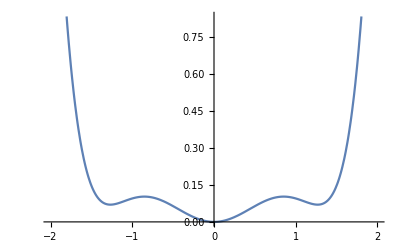

```mathematica
weakMVIglobalphi[z_]:=(z^2/3-z^4/3+z^6 2/21)
Plot[weakMVIglobalphi[z],{z,-2,2}]
```

```mathematica
WeakMVIGlobalForsaken[x_,y_]:=x *y+weakMVIglobalphi[x]-weakMVIglobalphi[y]
W[x_,y_]:=Evaluate@({1,1}*getW[WeakMVIGlobalForsaken]);
{xstar,ystar}={0,0};
Plot[weakMVIglobalphi[x],{x,-2,2}]
```

-Graphics-

x^2/3-x^4/3+(2 x^6)/21+x y-y^2/3+y^4/3-(2 y^6)/21

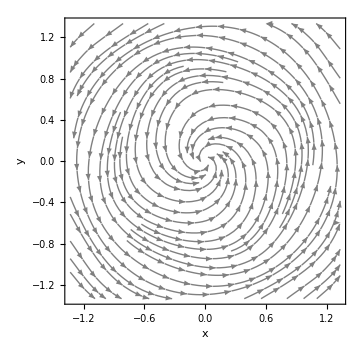

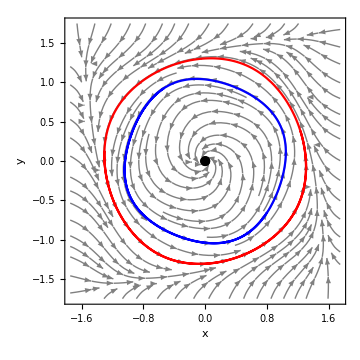

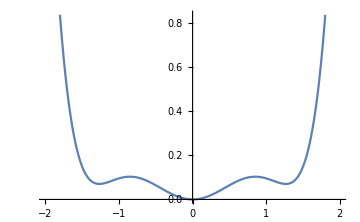

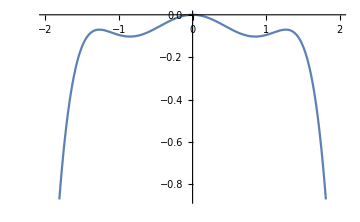

```mathematica
WeakMVIGlobalForsaken[x,y]
plotFlow[W,side=4/3]
plotMultipleTrajectories[W,{{1,1}},{{0,0.1}},10,25]
Plot[WeakMVIGlobalForsaken[x,ystar],{x,-2,2}]
Plot[WeakMVIGlobalForsaken[xstar,y],{y,-2,2}]
```

```mathematica
W[x_,y_]:=Evaluate@(getW[WeakMVIGlobalForsaken])
WeakMVIGlobalForsaken[x,y]
star={0,0};
sides=4/3;
cons=-sides<=x<=sides&&-sides<=y<=sides;
weakMVIcondition[x_,y_]:=Evaluate@(W[x,y]).({x,y}-star)/Norm[W[x,y]]^2;
J[x_,y_]:=Evaluate@(D[W[x,y],{{x,y}}]);
LocalLips[x_,y_]:=Evaluate@Norm[J[x,y],2];
```

x^2/3-x^4/3+(2 x^6)/21+x y-y^2/3+y^4/3-(2 y^6)/21

```mathematica
Show[
ContourPlot[weakMVIcondition[x,y],{x,-sides,sides},{y,-sides,sides},PlotLegends->Automatic,Contours->50,PlotLabel->"Local ρ"],plotMultipleTrajectories[W,{{1,1}},{{0,0.1}},25,50,7/4,True]]
```

-Graphics-

```mathematica
Show[
ContourPlot[-1/(2*LocalLips[x,y]),{x,-sides,sides},{y,-sides,sides},PlotLegends->Automatic,Contours->25,PlotLabel->"-1/(2|JFz|)"],
plotMultipleTrajectories[W,{{1,1}},{{0,0.1}},25,50,7/4,True]
]
```

-Graphics-

```mathematica
ρ=Assuming[{x∈Reals,y∈Reals},MinValue[{
weakMVIcondition[x,y]},{x,y}]//Simplify]
N[ρ]
```

Root-0.120Root[84428232354562005562500+7450229808545351276587500 #1+161840742140791256384935125 #1^2+281052191883976918460546850 #1^3-6415793336751733691869239351 #1^4+13233459874459563225122666004 #1^5+«21»+4530650008359019703629859722543104 #1^20-1808135227753402240813583158751232 #1^21-967407075439548897613616793219072 #1^22+1347159078258066668881294418255872 #1^23&,1]-0.11973199294086673

-0.119732

```mathematica
(*sides=11/10;*)
L=Assuming[{x∈Reals,y∈Reals},MaxValue[{
LocalLips[x,y],cons},{x,y}]//Simplify]
N[-1/(2L)]
```

(√(1/2 (74125591+9409 √59721901)))/2835

-0.165432

```mathematica
N[(√(1/2 (74125591+9409 √59721901)))/2835]
```

3.0224

## Proof of limit cycles

```mathematica
W[x_,y_]:=Evaluate@getW[WeakMVIGlobalForsaken]
```

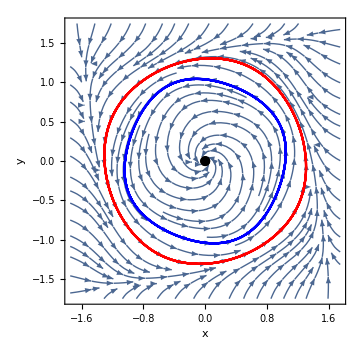

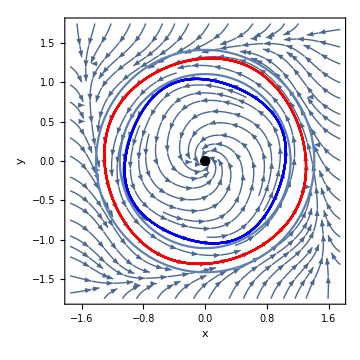

```mathematica
plotMultipleTrajectories[W,{{1,1}},{{0,0.1}},25,50,7/4,True]
Show[%, RegionPlot[ImplicitRegion[y^2+x^2==Sqrt[3/2],{x,y}]],RegionPlot[ImplicitRegion[y^2+x^2==2,{x,y}]]]
```

```mathematica
W[x,y]
%//MatrixForm//TeXForm
```

{(2 x)/3-(4 x^3)/3+(4 x^5)/7+y,-x+(2 y)/3-(4 y^3)/3+(4 y^5)/7}

\left(
\begin{array}{c}
 \frac{4 x^5}{7}-\frac{4 x^3}{3}+\frac{2 x}{3}+y \\
 -x+\frac{4 y^5}{7}-\frac{4 y^3}{3}+\frac{2 y}{3} \\
\end{array}
\right)

```mathematica
polar=TransformedField["Cartesian"->"Polar",-W[x,y],{x,y}->{r,theta}]//Simplify//Factor;
polar
%[[1]]//TeXForm
```

{-1/42 r (28-42 r^2+15 r^4-14 r^2 Cos[4 theta]+9 r^4 Cos[4 theta]),1/21 r (21-7 r^2 Sin[4 theta]+3 r^4 Sin[4 theta])}

-\frac{1}{42} r \left(9 r^4 \cos (4 \theta )-14 r^2 \cos (4 \theta )+15 r^4-42
   r^2+28\right)

```mathematica
Assuming[r==Sqrt[3/2],Simplify[polar]]
%[[1]]//TeXForm
```

{(5+3 Cos[4 theta])/(56 √6),1/28 √(3/2) (28-5 Sin[4 theta])}

\frac{3 \cos (4 \theta )+5}{56 \sqrt{6}}

So r’ is positive for any theta

```mathematica
Assuming[r==2,Simplify[polar]]
%[[1]]//TeXForm
```

{-4/21 (25+22 Cos[4 theta]),2+40/21 Sin[4 theta]}

-\frac{4}{21} (22 \cos (4 \theta )+25)

So r’ is negative for any theta

```mathematica
D[polar[[1]],r]
```

-1/24 r (-72 r+60 r^3-24 r Cos[4 theta]+36 r^3 Cos[4 theta])+1/24 (-20+36 r^2-15 r^4+12 r^2 Cos[4 theta]-9 r^4 Cos[4 theta])

## Proof of global Nash

```mathematica
WeakMVIGlobalForsaken[x,0]
WeakMVIGlobalForsaken[0,y]
```

x^2/3-x^4/3+(2 x^6)/21

-y^2/3+y^4/3-(2 y^6)/21

```mathematica
Minimize[{WeakMVIGlobalForsaken[x,0]},{x}]
Maximize[{WeakMVIGlobalForsaken[0,y]},{y}]
```

{0,{x→0}}

{0,{y→0}}

## Plotting

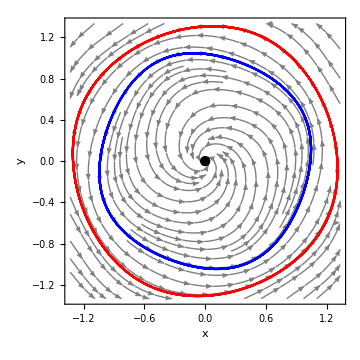

Figs/GlobalForsaken.png

```mathematica
plot=plotMultipleTrajectories[W,{{1,1}},{{0.0,0.1}},25,50,4/3,True]
Export["Figs/GlobalForsaken.png",%]
```